Modular Forms

```mathematica
fn :=x↦x^2
```

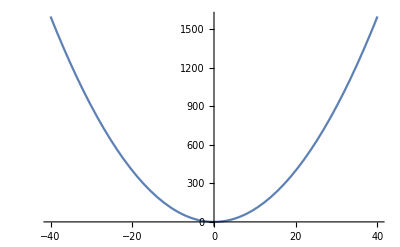

```mathematica
Plot[fn[x],{x,-40,40}]
```

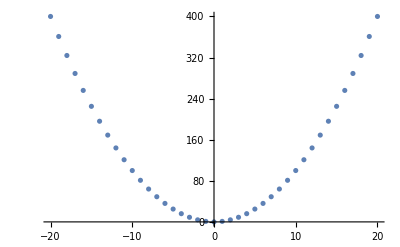

```mathematica
DiscretePlot[fn[x], {x,-20, 20}, Filling->None]
```

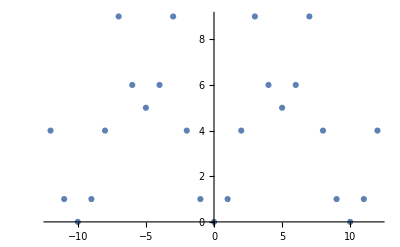

```mathematica
DiscretePlot[Mod[fn[x], 10], {x,-12, 12}, Filling->None]
```

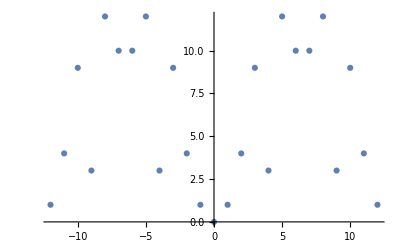

```mathematica
DiscretePlot[Mod[fn[x], 13], {x,-12, 12}, Filling->None]
```

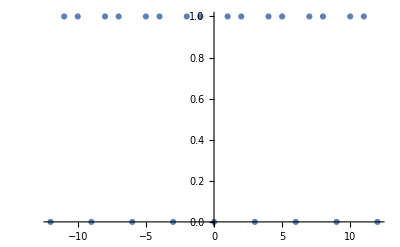

```mathematica
DiscretePlot[Mod[fn[x], 3], {x,-12, 12}, Filling->None]
```

```mathematica
fn3:={x,a,b,c,d}↦a*x^3+ b*x^2+c*x+d
```

```mathematica
Table[fn3[x,1,2,3,4]^(1/2), {x,1,20}]
```

{√10,√26,√58,4 √7,√194,√310,√466,2 √167,√922,√1234,√1610,2 √514,√2578,√3182,√3874,2 √1165,√5546,√6538,√7642,4 √554}

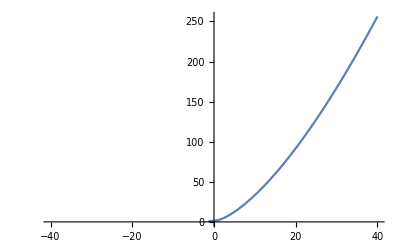

```mathematica
Plot[fn3[x,1,1,1,2]^(1/2),{x,-40,40}]
```

```mathematica
Manipulate[Plot[{fn3[x,a,b,c,d]^(1/2),fn3[x,a,b,c,d]^(1/3)},{x,-10,10}], {{a,1},-50, 50,1}, {{b,2},-500, 500}, {{c,-1},-50, 50}, {{d,-2},-500,500, 1}]
```

```mathematica
Manipulate[DiscretePlot[Mod[fn3[x,Mod[a,e],Mod[b,e],Mod[c,e],Mod[d,e]]^(1/2), e], {x,-e, e}, Filling->None], {{a,1},-50, 50,1}, {{b,2},-500, 500}, {{c,-1},-50, 50}, {{d,-2},-500,500, 1},{{e,10},1,2221, 1}]
```

```mathematica
Manipulate[DiscretePlot[Mod[fn3[x,a,b,c,d]^(1/2), e], {x,-e, e}, Filling->None], {a,-5, 5}, {b,-50, 50}, {c,-50, 50}, {d,-50,50}, {e,1,2221}]
```